## Init

```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*"])//TableForm
applyWithError[fct_,arg_]:=Module[{i,total,direction},
total=0;
(* calculate gauss error *)
direction=Table[0,{i,1,Length[arg]}];
For[i=1,i≤Length[arg],i++,
direction⟦i⟧=1;
total+=(((Derivative@@direction)[fct])@@arg⟦1;;,1⟧)^2*arg⟦i,2⟧^2;
direction⟦i⟧=0;
];
{fct@@arg⟦1;;,1⟧,Sqrt[total]}
]
weightedMean[vals_]:={Sum[vals⟦i,1⟧/vals⟦i,2⟧,{i,1,Length[vals]}]/Sum[1/vals⟦i,2⟧,{i,1,Length[vals]}],Sqrt[1/(Sum[1/vals⟦i,2⟧,{i,1,Length[vals]}])^2]}
```

data\kalibrier.nb
data\M7_15C.TXT
data\M7_25C.TXT
data\M7_38C.TXT
data\M7ABS.TXT
data\M7_AN15.TX
data\M7_AN25.TX
data\M7_AN38.TX
data\M7EMSNON.TXT
data\M7EMSVES.TXT
data\M7_LT25.TX
data\M7_LT38.TX
data\mini.ods
data\placeholder.txt
data\temperatur2.ods
data\temperatur.ods

```mathematica
read[n_]:=Module[{dat},
str=OpenRead[files⟦n⟧];
dat={{},{}};
dat⟦1⟧=ReadList[str,Number,4];
ReadList[str,String,18];
dat⟦2⟧=ReadList[str,Number];
dat=Table[{dat⟦1⟧⟦3⟧+(i-1)*(dat⟦1⟧⟦4⟧-dat⟦1⟧⟦3⟧)/dat⟦1⟧⟦1⟧, dat⟦2⟧⟦i⟧},{i,1,Length@dat⟦2⟧}]
]
abs=read[5];
ves=read[10];
non={#⟦1⟧,#⟦2⟧/100}&/@read[9];
```

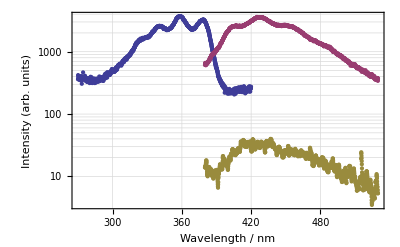

```mathematica
ListLogPlot[{abs,ves,non},Frame->True,Axes->None,FrameLabel->{"Wavelength / nm","Intensity (arb. units)"},GridLines->Automatic]
```

## fits, spectra

```mathematica
lg[x_,a_,s_,p_,x0_]:=a*E^(-s*p*Log[2]*(x-x0)^2)/(1+s*(1-p)(x-x0)^2);
fita=NonlinearModelFit[abs,
r1*x+r2+
lg[x,a1,s1,p,x01]+
lg[x,a2,s2,p,x02]+
lg[x,a3,s3,p,x03]+
lg[x,a4,s4,p,x04],
{{r1,0},{r2,0},{p,0.5},
{a1,2000},{s1,0.1},{x01,320},
{a2,2000},{s2,0.1},{x02,340},
{a3,2000},{s3,0.1},{x03,360},
{a4,2000},{s4,0.1},{x04,380}},
x
]
fita["ParameterConfidenceIntervalTable"]
```

FittedModel[-87.3698+(2825.87 2^(«1»))/(1+0.0288596 «1»)+«1»+«1»+(«1»)/(1+«1»)-0.27336 x]

| Estimate | Standard Error | Confidence Interval
r1 | -0.27336 | 0.177173 | {-0.620897,0.0741764}
r2 | -87.3698 | 79.2975 | {-242.917,68.1773}
p | -0.0164574 | 0.000472533 | {-0.0173843,-0.0155305}
a1 | 1234.48 | 41.4474 | {1153.17,1315.78}
s1 | 0.00367388 | 0.000314569 | {0.00305683,0.00429093}
x01 | 326.899 | 0.510689 | {325.897,327.9}
a2 | 1349.79 | 51.572 | {1248.63,1450.95}
s2 | 0.0261894 | 0.00223288 | {0.0218095,0.0305694}
x02 | 340.557 | 0.091305 | {340.378,340.736}
a3 | 3145.75 | 13.8094 | {3118.66,3172.84}
s3 | 0.0134756 | 0.000287961 | {0.0129108,0.0140405}
x03 | 358.587 | 0.0393695 | {358.51,358.665}
a4 | 2825.87 | 13.9504 | {2798.51,2853.23}
s4 | 0.0283923 | 0.000587759 | {0.0272394,0.0295453}
x04 | 377.958 | 0.0302937 | {377.898,378.017}

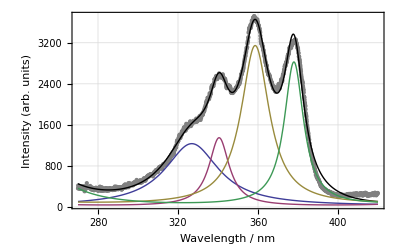

```mathematica
Show[
ListPlot[abs,PlotStyle->Gray],
Plot[Normal@fita,{x,270,420},PlotStyle->Black],
Plot[{lg[x,1234.48,0.00367388,-0.0164574,326.899],
lg[x,1349.79,0.0261894,-0.0164574,340.557],
lg[x,3145.75,0.0134756,-0.0164574,358.587],
lg[x,2825.87,0.0283923,-0.0164574,377.958]},{x,270,420},PlotRange->All],
Frame->True,Axes->None,FrameLabel->{"Wavelength / nm","Intensity (arb. units)"},GridLines->Automatic
]
```

```mathematica
fitv=NonlinearModelFit[ves,
r1*x+r2+
lg[x,a1,s1,p,x01]+
lg[x,a2,s2,p,x02]+
lg[x,a3,s3,p,x03]+
lg[x,a4,s4,p,x04],
{{r1,0},{r2,0},{p,0.5},
{a1,2000},{s1,0.1},{x01,400},
{a2,2000},{s2,0.1},{x02,425},
{a3,2000},{s3,0.1},{x03,450},
{a4,2000},{s4,0.1},{x04,490}},
x
]
fitv["ParameterConfidenceIntervalTable"]
```

FittedModel[-147.855+(584.217 2^(«1»))/(1+0.00189521 «1»)+«1»+«1»+(«1»)/(1+«1»)+0.508666 x]

| Estimate | Standard Error | Confidence Interval
r1 | 0.508666 | 0.0503835 | {0.409836,0.607497}
r2 | -147.855 | 4.94155 | {-157.548,-138.161}
p | 1.12347×10^-9 | 0.0042762 | {-0.00838803,0.00838803}
a1 | 1451.53 | 7.34487 | {1437.12,1465.94}
s1 | 0.0102415 | 0.000153328 | {0.00994075,0.0105423}
x01 | 403.744 | 0.0344498 | {403.676,403.811}
a2 | 2765.97 | 14.2026 | {2738.12,2793.83}
s2 | 0.00449883 | 0.0000644482 | {0.00437241,0.00462525}
x02 | 426.858 | 0.0317485 | {426.795,426.92}
a3 | 1565.68 | 14.9263 | {1536.4,1594.96}
s3 | 0.00362688 | 0.0000923707 | {0.00344569,0.00380807}
x03 | 454.014 | 0.0675216 | {453.881,454.146}
a4 | 584.217 | 13.0049 | {558.707,609.727}
s4 | 0.00189521 | 0.0000906629 | {0.00171737,0.00207305}
x04 | 482.985 | 0.313198 | {482.371,483.599}

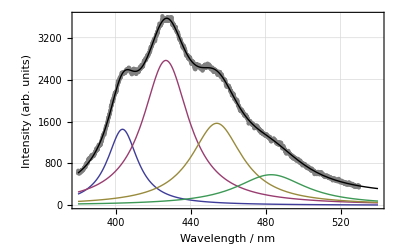

```mathematica
Show[
ListPlot[ves,PlotStyle->Gray],
Plot[Normal@fitv,{x,380,540},PlotStyle->Black],
Plot[{lg[x,1451.5,0.01024,0,403.744],
lg[x,2766,0.0044988,0,426.858],
lg[x,1566,0.00362688,0,454.014],
lg[x,584.2,0.00189521,0,482.985]},{x,380,540},PlotRange->All],
Frame->True,Axes->None,FrameLabel->{"Wavelength / nm","Intensity (arb. units)"},GridLines->Automatic
]
```

```mathematica
fitn=NonlinearModelFit[non,
r1*x+r2+
lg[x,a1,0.0102,0,403.7]+
lg[x,a2,0.00450,0,426.86]+
lg[x,a3,0.00363,0,454.0]+
lg[x,a4,0.00190,0,482.985],
{{r1,0},{r2,0},
{a1,20},
{a2,20},
{a3,20},
{a4,20}},
x
]
fitn["ParameterConfidenceIntervalTable"]
```

FittedModel[10.429+7.1912/(1+0.0019 («1»)^2)+(«18»)/(1+«1»)+«1»+(«18»)/(1+«7» «1»)-0.0112866 x]

| Estimate | Standard Error | Confidence Interval
r1 | -0.0112866 | 0.0033766 | {-0.01791,-0.00466325}
r2 | 10.429 | 1.64029 | {7.21151,13.6465}
a1 | 8.89744 | 0.516956 | {7.8834,9.91147}
a2 | 24.6736 | 0.375603 | {23.9368,25.4104}
a3 | 11.5179 | 0.345326 | {10.8405,12.1953}
a4 | 7.1912 | 0.397938 | {6.41063,7.97178}

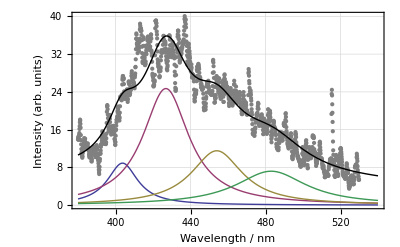

```mathematica
Show[
ListPlot[non,PlotStyle->Gray],
Plot[Normal@fitn,{x,380,540},PlotStyle->Black],
Plot[{lg[x,8.90,0.01024,0,403.744],
lg[x,24.7,0.0044988,0,426.858],
lg[x,11.52,0.00362688,0,454.014],
lg[x,7.19,0.00189521,0,482.985]},{x,380,540},PlotRange->All],
Frame->True,Axes->None,FrameLabel->{"Wavelength / nm","Intensity (arb. units)"},GridLines->Automatic
]
```

```mathematica
n=(#1+#2+#3+#4)&~applyWithError~{{8.897,1.02},{24.674,0.8},{11.518,0.68},{7.191,0.78}}
v=(#1+#2+#3+#4)&~applyWithError~{{1451.53,14},{2766,27},{1566,26},{584,25}}
(#2/#1)&~applyWithError~{n,v}
```

{52.28,1.65867}

{6367.53,√2226}

{121.797,3.96819}

## init anisotropy

```mathematica
readA[n_]:=Module[{dat},
str=OpenRead[files⟦n⟧];
ReadList[str,String,3];
dat=ReadList[str,{Number,Number,Number,Number}]
]
readwtf[n_]:=Module[{dat},
str=OpenRead[files⟦n⟧];
ReadList[str,String,3];
dat= ReadList[str,{Number,Number,Number,Number,Number}]⟦1;;,2;;5⟧
]
a15=readA[2];
a25=readA[3];
a38=readwtf[4];
```

```mathematica
sum={a15⟦1,1⟧};
For[i=2,i<=Length@a15,++i,
AppendTo[sum,sum⟦i-1⟧+a15⟦i,1⟧];
]
```

```mathematica
stuff[dat_]:=Module[{fit1,fit2,w},
w=Table[Abs[(sum⟦i⟧^3)/(0.0000001+dat⟦i,3⟧*(dat⟦i,3⟧+sum⟦i⟧))],{i,40,Length@sum}];
fit1=NonlinearModelFit[(dat⟦1;;,3⟧/(sum+0.00000001))⟦40;;⟧,a E^(-b x)+r0,{{a,0.001},{b,0.001},{r0,0}},x,
Weights->w];
w=Table[Abs[(sum⟦i⟧^3)/(0.0000001+dat⟦i,4⟧*(dat⟦i,4⟧+sum⟦i⟧))],{i,40,Length@sum}];
fit2=NonlinearModelFit[(dat⟦1;;,4⟧/(sum+0.00000001))⟦40;;⟧,a E^(-b x)+r0,{{a,0.001},{b,0.001},{r0,0}},x,
Weights->w];
Print["b1= "<>ToString[({#⟦1⟧+#⟦2⟧,Abs[#⟦2⟧-#⟦1⟧]}/2)&@(fit1["ParameterConfidenceIntervals"]⟦2⟧)]];
Print["b2= "<>ToString[({#⟦1⟧+#⟦2⟧,Abs[#⟦2⟧-#⟦1⟧]}/2)&@fit2["ParameterConfidenceIntervals"]⟦2⟧]];
Print[fit1["RSquared"]];
Print@Show[
ListLogPlot[{(dat⟦1;;,3⟧/sum),(dat⟦1;;,4⟧/sum)},Joined->True,PlotRange->All,Frame->True,Axes->None,GridLines->Automatic,FrameLabel->{"Channel","Intensity (arb. units)"},ImageSize->350],
LogPlot[{Normal@fit1/.x->(y-50),Normal@fit2/.x->(y-50)},{y,0,255}]
];
{fit1,fit2}
]
```

b1= {0.00843907, 0.00253561}

b2= {0.0062813, 0.00303384}

0.961958

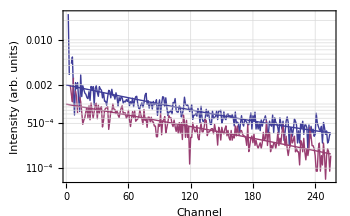

b1= {0.00650709, 0.00218178}

b2= {0.00874173, 0.00258256}

0.970146

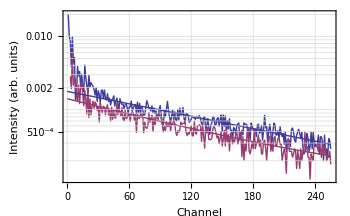

b1= {0.00874829, 0.00263535}

b2= {0.00996938, 0.00286615}

0.951823

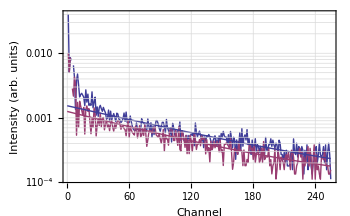

{{FittedModel[0.000139429+0.00121122 ⅇ^(-0.00843907 x)],FittedModel[-0.0000427113+0.000757807 ⅇ^(-0.0062813 x)]},{FittedModel[-2.386×10^-6+0.00128494 ⅇ^(-0.00650709 x)],FittedModel[0.0000915772+0.000852395 ⅇ^(-0.00874173 x)]},{FittedModel[0.0000768071+0.000943204 ⅇ^(-0.00874829 x)],FittedModel[0.000086781+0.000709833 ⅇ^(-0.00996938 x)]}}

```mathematica
fits=stuff/@{a15,a25,a38}
```

```mathematica
fits⟦1,1⟧["EstimatedVariance"]
```

1.20453

```mathematica
FullSimplify@(#1/#2&~applyWithError~{{m,Sqrt@m},{t,Sqrt[t]}})
```

{m/t,√((m (m+t))/t^3)}